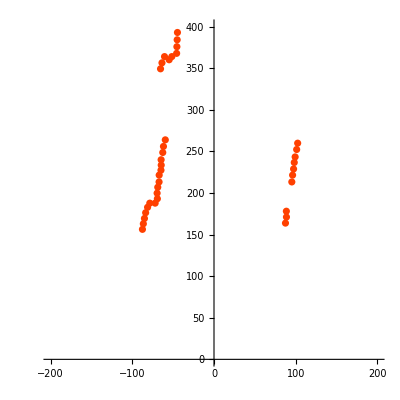
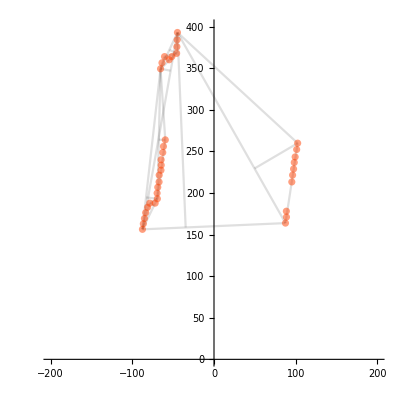
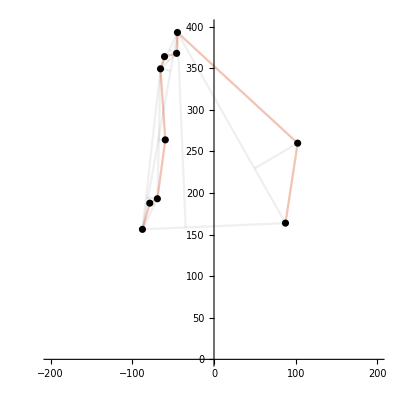
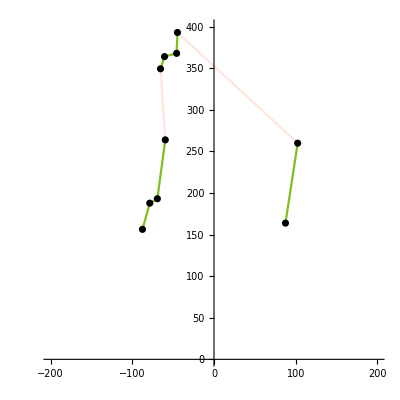

```mathematica
frameA = {{-87.553008, 156.3}, {-86.4554445, 163.}, {-85.1054589, 169.4}, {-83.63416365, 176.3}, {-81.2778156, 182.8}, {-78.5697921, 187.8}, {-71.9949141, 187.8}, {-69.29441775, 193.1}, {-69.6002301, 199.8}, {-68.8139055, 206.9}, {-67.208697, 213.3}, 
    {-67.07828475, 221.5}, {-64.8843831, 227.4}, {-64.5811965, 233.5}, {-64.69848, 240.}, {-62.6903064, 248.7}, {-61.841664, 256.}, {-59.59244655, 263.9}, {-65.42511255, 349.3}, {-63.6534315, 356.5}, {-60.53229, 364.}, {-54.8561187, 360.2}, 
    {-51.611742, 364.}, {-45.72463545, 367.9}, {-45.40289355, 375.9}, {-45.0603207, 384.2}, {-44.7165225, 393.}, {102.36486375, 259.9}, {101.13811335, 252.3}, {99.2747061, 243.4}, {98.19937395, 236.7}, {97.36753635, 228.9}, {96.158466, 221.5}, 
    {95.21232075, 213.3}, {88.5409902, 178.1}, {88.6551228, 171.1}, {87.4532295, 163.8}}; 

frameB = {{-88.393248, 157.8}, {-86.8797657, 163.8}, {-86.1032439, 170.2}, {-83.9427768, 176.3}, {-81.2778156, 182.8}, {-75.3737292, 184.8}, {-71.9949141, 187.8}, {-71.756496, 195.2}, {-71.10898605, 202.1}, {-69.6786525, 209.5}, {-68.500566, 217.4}, 
    {-68.0153274, 225.9}, {-67.033647, 233.5}, {-65.95884, 240.}, {-65.26196595, 246.9}, {-64.0767024, 254.2}, {-59.615028, 258.}, {-69.9625836, 317.2}, {-69.6635982, 326.2}, {-69.823944, 332.4}, {-68.836662, 339.}, {-67.7961648, 345.8}, 
    {-64.901538, 356.5}, {-61.1572185, 356.5}, {-55.4866488, 360.2}, {-49.1813478, 360.2}, {-47.7504891, 384.2}, {-45.404469, 393.}, {100.380672, 256.}, {98.82430245, 248.7}, {97.73514135, 241.7}, {96.3009567, 235.1}, {95.76477855, 228.9}, 
    {94.1772501, 218.7}, {93.6829089, 210.7}, {91.8161757, 203.3}, {91.4503212, 196.4}, {89.8944768, 188.8}, {88.9576092, 182.8}, {88.1198199, 175.4}, {87.0646185, 168.6}, {85.942548, 161.5}}; 

GetDistanceSegment[segmentAB_, pointC_] :=(
offset := segmentAB[[1]];
vABn := Normalize[segmentAB[[2]] - segmentAB[[1]]];
{pointC, vABn . (pointC - segmentAB[[1]]) * vABn + segmentAB[[1]]}
)

l01 = {frameA[[1]],frameA[[-1]]}; d01 = GetDistanceSegment[l01, frameA[[27]]];
l02 = {frameA[[1]],frameA[[27]]}; d02 = GetDistanceSegment[l02, frameA[[19]]];
l03 = {frameA[[27]],frameA[[-1]]}; d03 = GetDistanceSegment[l03, frameA[[28]]];
l04 = {frameA[[1]],frameA[[19]]}; d04 = GetDistanceSegment[l04, frameA[[8]]];
l05 = {frameA[[19]],frameA[[27]]}; d05 = GetDistanceSegment[l05, frameA[[24]]];
l06 = {frameA[[27]],frameA[[28]]};
l07 = {frameA[[28]],frameA[[-1]]};
l08 = {frameA[[1]],frameA[[8]]}; d08 = GetDistanceSegment[l08, frameA[[6]]];
l09 = {frameA[[8]],frameA[[19]]}; d09 = GetDistanceSegment[l09, frameA[[18]]];
l10 = {frameA[[19]],frameA[[24]]}; d10 = GetDistanceSegment[l10, frameA[[21]]];
l11 = {frameA[[24]],frameA[[27]]};
l12 = {frameA[[1]],frameA[[6]]};
l13 = {frameA[[6]],frameA[[8]]};
l14 = {frameA[[8]],frameA[[18]]};
l15 = {frameA[[18]],frameA[[19]]};
l16 = {frameA[[19]],frameA[[21]]};
l17 = {frameA[[21]],frameA[[24]]};

(* --- Colors --- *)
Black12 = RGBColor[0,0,0,0.125]; Black06 = RGBColor[0,0,0,0.0625]; Terra = RGBColor[1,0.25,0,1];Terra50 = RGBColor[1,0.25,0,0.5];Terra25 = RGBColor[1,0.25,0,0.25]; Terra12 = RGBColor[1,0.25,0,0.125]; Olive = RGBColor[0.5,0.75,0.125]; 
(* --- ViewPrefs --- *)


Row[{
Show[ListPlot[{frameA}, AxesOrigin-> {0, 0}, AspectRatio-> 1, PlotRange-> {{-200, 200}, {0, 400}}, ImageSize-> {400, 460};  PlotStyle-> Terra]],
Show[
ListLinePlot[{l01}, AxesOrigin-> {0, 0}, AspectRatio-> 1, PlotRange-> {{-200, 200}, {0, 400}}, ImageSize-> {400, 460}; PlotStyle->Black12], ListLinePlot[{d01},PlotStyle->Black12],
ListLinePlot[{l02},PlotStyle->Black12], ListLinePlot[{d02},PlotStyle->Black12],
ListLinePlot[{l03},PlotStyle->Black12], ListLinePlot[{d03},PlotStyle->Black12],
ListLinePlot[{l04},PlotStyle->Black12], ListLinePlot[{d04},PlotStyle->Black12],
ListLinePlot[{l05},PlotStyle->Black12], ListLinePlot[{d05},PlotStyle->Black12],
ListLinePlot[{l06},PlotStyle->Black12],
ListLinePlot[{l07},PlotStyle->Black12],
ListLinePlot[{l08},PlotStyle->Black12], ListLinePlot[{d08},PlotStyle->Black12],
ListLinePlot[{l09},PlotStyle->Black12], ListLinePlot[{d09},PlotStyle->Black12],
ListLinePlot[{l10},PlotStyle->Black12], ListLinePlot[{d10},PlotStyle->Black12],
ListLinePlot[{l11},PlotStyle->Black12],
ListLinePlot[{l12},PlotStyle->Black12],
ListLinePlot[{l13},PlotStyle->Black12],
ListLinePlot[{l14},PlotStyle->Black12],
ListLinePlot[{l15},PlotStyle->Black12],
ListLinePlot[{l16},PlotStyle->Black12],
ListLinePlot[{l17},PlotStyle->Black12],
ListPlot[{frameA},PlotStyle-> Terra50]
],
Show[
ListLinePlot[{l01}, AxesOrigin-> {0, 0}, AspectRatio-> 1, PlotRange-> {{-200, 200}, {0, 400}}, ImageSize-> {400, 460}; PlotStyle->Black06], ListLinePlot[{d01},PlotStyle->Black06],
ListLinePlot[{l02},PlotStyle->Black06], ListLinePlot[{d02},PlotStyle->Black06],
ListLinePlot[{l03},PlotStyle->Black06], ListLinePlot[{d03},PlotStyle->Black06],
ListLinePlot[{l04},PlotStyle->Black06], ListLinePlot[{d04},PlotStyle->Black06],
ListLinePlot[{l05},PlotStyle->Black06], ListLinePlot[{d05},PlotStyle->Black06],
ListLinePlot[{l06},PlotStyle->Black06],
ListLinePlot[{l07},PlotStyle->Black06],
ListLinePlot[{l08},PlotStyle->Black06], ListLinePlot[{d08},PlotStyle->Black06],
ListLinePlot[{l09},PlotStyle->Black06], ListLinePlot[{d09},PlotStyle->Black06],
ListLinePlot[{l10},PlotStyle->Black06], ListLinePlot[{d10},PlotStyle->Black06],
ListLinePlot[{l11},PlotStyle->Black06],
ListLinePlot[{l12},PlotStyle->Black06],
ListLinePlot[{l13},PlotStyle->Black06],
ListLinePlot[{l14},PlotStyle->Black06],
ListLinePlot[{l15},PlotStyle->Black06],
ListLinePlot[{l16},PlotStyle->Black06],
ListLinePlot[{l17},PlotStyle->Black06], 
ListLinePlot[{l12}, AxesOrigin-> {0, 0}, AspectRatio-> 1, PlotRange-> {{-200, 200}, {0, 400}}, ImageSize->{400, 460}; PlotStyle->Terra25],
ListLinePlot[{l13},PlotStyle->Terra25], ListLinePlot[{l14},PlotStyle->Terra25], ListLinePlot[{l15},PlotStyle->Terra25], 
ListLinePlot[{l16},PlotStyle->Terra25], ListLinePlot[{l17},PlotStyle->Terra25],ListLinePlot[{l11},PlotStyle->Terra25],
ListLinePlot[{l06},PlotStyle->Terra25],ListLinePlot[{l07},PlotStyle->Terra25],
ListPlot[{frameA[[1]], frameA[[6]], frameA[[8]], frameA[[18]], frameA[[19]], frameA[[21]], frameA[[24]], frameA[[27]], frameA[[28]], frameA[[-1]]},PlotStyle-> Black]
],
Show[
ListLinePlot[{l12}, AxesOrigin-> {0, 0}, AspectRatio-> 1, PlotRange-> {{-200, 200}, {0, 400}}, ImageSize->{400, 460}; PlotStyle->Olive],
ListLinePlot[{l13},PlotStyle->Olive], ListLinePlot[{l14},PlotStyle->Olive], ListLinePlot[{l15},PlotStyle->Terra12], 
ListLinePlot[{l16},PlotStyle->Olive], ListLinePlot[{l17},PlotStyle->Olive],ListLinePlot[{l11},PlotStyle->Olive],
ListLinePlot[{l06},PlotStyle->Terra12],ListLinePlot[{l07},PlotStyle->Olive],
ListPlot[{frameA[[1]], frameA[[6]], frameA[[8]], frameA[[18]], frameA[[19]], frameA[[21]], frameA[[24]], frameA[[27]], frameA[[28]], frameA[[-1]]},PlotStyle-> Black]
]
}(*, AnimationRunning->False*)]

(*Remove["Global`*"]*)
```